# 2. Relativistic Gravity Train

## 2.1 Electrostatic Gravity Train

## 2.2 Special Relativistic Gravity Train

The Lorentz law in covariant version give us the work-energy and the equations of motion:

```mathematica
m(d^2 x^1)/(d τ^2) = q E^1 U^0
```

and after using Gauss law we get

```mathematica
E(r)=(4π)/3 Subscript[ρ, c] r r̂
```

Using both equations we have the next relation

```mathematica
m(d U^1)/(d τ)= - m ω^2 x^1 U^0
```

we also have the next equation

```mathematica
m(d U^0)/(d τ)= - m ω^2 x^1 dx^1/dτ
```

using both we get the coupled equation for x^1  ,

```mathematica
(d^2 x^1)/dτ^2+E x^1=1/2 x^3
```

### 2.2.1 Energy Considerations

The energy equation associated to Duffing equation is the following:

```mathematica
1/2(dx/dτ)^2+Subscript[V, Eff](x) = E
```

where the effective potential is

```mathematica
Subscript[V, eff](x) = 1/2 E x^2-1/8 x^4=1/2(1 + 1/2 R^2)x^2-1/8 x^4
```

which now we are going to define and plot

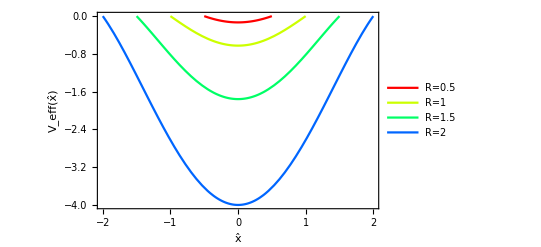

```mathematica
V sr[R_,x_]:=Piecewise[{{0.5 (1+0.5 R^2)x^2 - 0.125 x^4 - 0.5(1+0.25 R^2) R^2,Abs[x]≤ R},{None,Abs[x]≥ R}}]
SRPotential = Plot[{V sr[0.5,x],V sr[1,x],V sr[1.5,x],V sr[2,x]},{x,-2,2},
PlotLegends->Placed[{"R=0.5","R=1","R=1.5","R=2" },{Left,Bottom}],
PlotStyle->Table[Hue[n],{n,0,.8,0.2}],
Frame->True,
FrameLabel->{"x̂","V_eff(x̂)"}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/2-Relativistic Gravity Train/Plots/2-Effecive_Potential_SR_m.pdf",SRPotential];
```

### 2.2 .2 Proper Velocity

### 2.2.3 Traversal Times

The solutions to Duffing equation can be written in terms of the elliptic integral of the first kind

```mathematica
τ=2/SubPlus[R] F(x/R,R/SubPlus[R])
```

let’s plot it here as a function of R

```mathematica
Rp[R_]:= Sqrt[4+R^2];
```

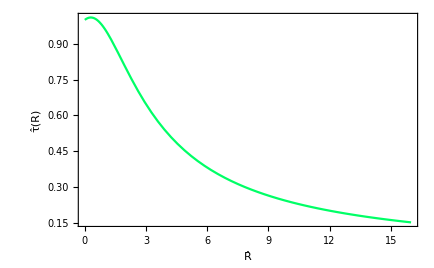

```mathematica
τ[R_,x_]:= 2/Rp[R] EllipticF[x/R,R/Rp[R]]
PropertTimes = Plot[τ[R,R],{R,0,16},
PlotStyle->Hue[0.4],
Frame->True,
FrameLabel->{"R̂","τ̂(R)"}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/2-Relativistic Gravity Train/Plots/4-Proper_times.pdf",PropertTimes];
```

### 2.24 Proper Trajectory

Inverting to get position as a function of time, we get

```mathematica
x(τ)= R sn(SubPlus[R]/2 τ,R/SubPlus[R])
```

where sn(x,y) is the Jacobi elliptic function, and where the radius R_+ is defined as

```mathematica
SubPlus[R]=√(4+R^2)
```

The following is the code to define and print this solutions:

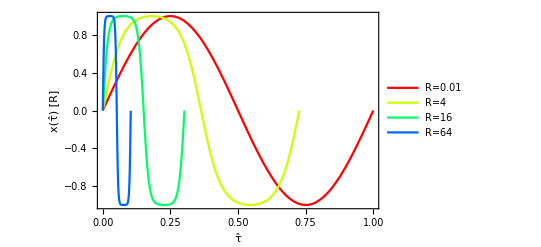

```mathematica
Rp[R_]:= Sqrt[4+R^2];
x[τ_,R_]:=Piecewise[{{JacobiSN[Rp[R] Pi τ, R/Rp[R]], τ<FunctionPeriod[JacobiSN[x, R/Rp[R]],x]/(Rp[R] Pi)},{None,τ≥ FunctionPeriod[JacobiSN[x, R/Rp[R]],x]/(Rp[R] Pi)}}]
SRProperTrajectory=Plot[{x[τ,0],x[τ,4],x[τ,16],x[τ,64]},{τ,0,1},
PlotLegends->Placed[{"R=0.01","R=4","R=16","R=64" },{Right,Top}],
PlotStyle->Table[Hue[n],{n,0,.8,0.2}],
Frame->True,
FrameLabel->{"τ̂","x(τ̂) [R]"}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/2-Relativistic Gravity Train/Plots/2-SR_Proper_Trajectory.pdf",SRProperTrajectory];
```

This apparently simple graph shows a very interesting feature, and a logical one in terms of Einsteins relativity : when R is big, which means almost relativistic velocities, the observer inside the train seems to spend more times near the borders of the path, and he or she sees the Earth moving faster when it approaches the center .

### 2.2.4 Coordinate Trajectory

This one is

```mathematica
t(x)=SubPlus[R] E(x/R,R/SubPlus[R]) - τ(x),
```

and here we defined in mathematica:

```mathematica
t[R_,x_]:= Rp[R] EllipticE[x/R,R/Rp[R]]-τ[R,x]
```

with this one, we can plot the times as a function of the radius

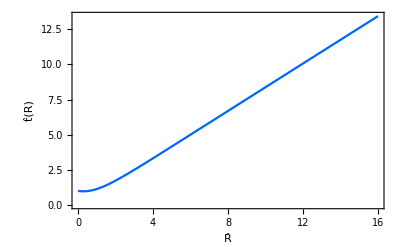

```mathematica
CoordinateTimes =Plot[t[R,R],{R,0,16},
PlotStyle->Hue[0.6],
Frame->True,
FrameLabel->{"R̂","t̂(R)"}]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/2-Relativistic Gravity Train/Plots/5-Coordinate_times.pdf",CoordinateTimes];
```

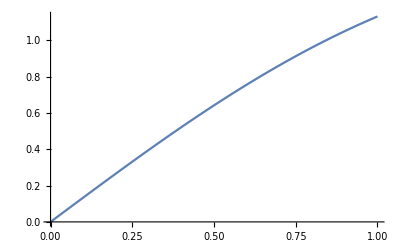

```mathematica
Plot[t[R,x],{x,0,R}]
```

To see the trajectory, let’s instead solve numerically the DE

```mathematica
En[R_]:=1+0.5 R^2
R = 1;
solution = NDSolve[{x'[tt]^2+ 1/((En[R]-0.5 x[tt]^2)^2)==1 ,x[0]== 0},x,{tt,0,t[R,R]}]
```

NDSolve::ndnl: Endpoint t[1.,1.] in {tt,0.,t[1.,1.]} is not a real number.

NDSolve[{1/((1.5-0.5 x[tt]^2)^2)+x'[tt]^2==1,x[0]==0},x,{tt,0,t[1,1]}]

```mathematica
Rarray=x[t[R,R]]/.solution
```

{0.778789,-0.778789}

```mathematica
xarray[[2]]=xarray[[xarray[[1]]+xa
```

0.778789

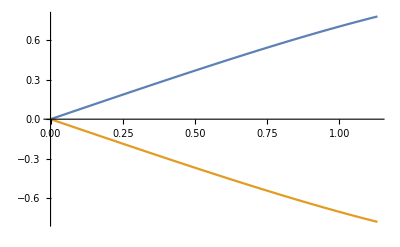

```mathematica
Plot[Evaluate[x[tt]/.solution],{tt,0,t[R,R]}]
```

```mathematica
t[R,R]//N
```

1.13243

```mathematica
2t[R,R]//N
```

2.26485

## 2.3 General Relativistic Gravity Train

### 2.3.1 Null Trajectory

For a null geodesic, let’s solve the equation:

```mathematica
R=0.2;
sol=NDSolve[{r'[t]== 3/2 √((1-2 r[t]^2)(1-2 R^2))+r[t]^2-1/2,r[0]==-1/(√2)},r[t],{t,0,2}]
```

{{r[t]→InterpolatingFunction[…][t]}}

Let’s evaluated at some point

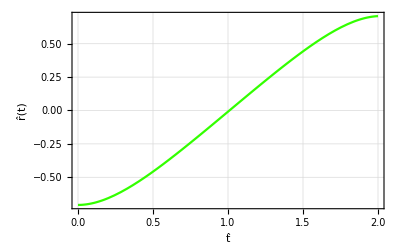

```mathematica
Null trajectory=Plot[Evaluate[r[t]/.sol],{t,0,2},
FrameLabel->{ {"r̂(t)", None},{"t̂",None}},
GridLines->Automatic,
Frame->True,
PlotStyle->Hue[0.3],
PlotTheme->"Scientific"]
```

### 2.3.2 Massive Trajectory

General Relativistic Potential:

```mathematica
Em[R_]:=√(1-2 R)
V GR[r_,R_]:= 1
```

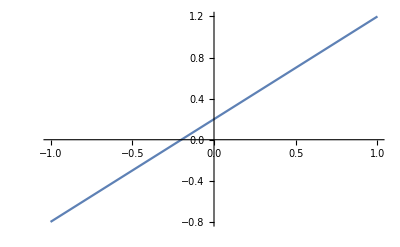

```mathematica
Plot[V GR[r,0.2],{r,-R,R}]
```

For a massive particle trajectory, the equation to solve is

```mathematica
dr/dτ= E x (√((5-x)(x-1)))/(x-3)
```

with

```mathematica
x = (√(1-2 r^2))/E= (√(1-2 r^2))/(√(1-2 R^2))
```

here we implement it

```mathematica
T = 1.5;
x[r_,R_]:= Sqrt[1-2*r^2]/Sqrt[1-2*R^2]
R=0.2;
Mtr1 = NDSolve[{r'[t]== Em[R]*Sqrt[(5 - x[r[t],R])(x[r[t],R]-1)]/(3-x[r[t],R]) ,r[0]==0.},r[t],{t,0,T}]
```

{{r[t]→InterpolatingFunction[…][t]}}

```mathematica
r1={0,Evaluate[r[0 ]/.Mtr1]}
```

{0,{r[0]}}

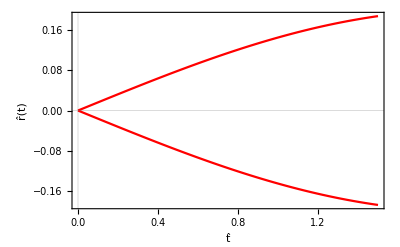

```mathematica
Plot[{r1[t],-r1[t]},{t,0,1.5},
FrameLabel->{{"r̂(t)", None},{"t̂",None}},
Frame->True,
PlotStyle->Hue[0],
PlotTheme->"Scientific"]
```

```mathematica
Mtr2 = NDSolve[{r'[t]== x[r[t],0]*Sqrt[(5 - x[r[t],R])(x[r[t],R]-1)]/(x[r[t],R]-3) ,r[T]==0.2},r[t],{t,T,2T}]
```

{{r[t]→InterpolatingFunction[…][t]}}

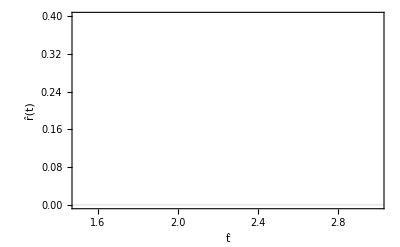

```mathematica
Plot[{Evaluate[r[t]/.Mtr2]},{t,T,2 T},
FrameLabel->{{"r̂(t)", None},{"t̂",None}},
Frame->True,
PlotStyle->Green,
PlotTheme->"Scientific"]
```

```mathematica
R=0.6;
T = 1.;
Mtr3 = NDSolve[{r'[t]== x[r[t],0]*Sqrt[(5 - x[r[t],R])(x[r[t],R]-1)]/(3-x[r[t],R]) ,r[0]==0},r[t],{t,-T,T}]
```

{{r[t]→InterpolatingFunction[…][t]}}

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

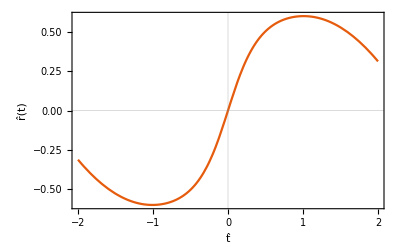

```mathematica
Plot[{Evaluate[r[t]/.Mtr3]},{t,-2,2 },
FrameLabel->{{"r̂(t)", None},{"t̂",None}},
Frame->True,
PlotTheme->"Scientific"]
```